# Bicubic Spline Interpolation

This setup cubic splines and scales them for use in the rays code.

## File

```mathematica
file=SystemDialogInput["FileOpen"]
```

/Users/m4c/Research/test.nc

```mathematica
psi=Normal[Import[file,{"Datasets","psi"}]];
rdim=Import[file,{"Datasets","rdim"}];
zdim=Import[file,{"Datasets","zdim"}];
rleft=Import[file,{"Datasets","rleft"}];
zmid=Import[file,{"Datasets","zmid"}];
psibry=Import[file,{"Datasets","psibry"}];
fpol=Normal[Import[file,{"Datasets","fpol"}]];
pres=Normal[Import[file,{"Datasets","pres"}]];
rho=Normal[Import[file,{"Datasets","rho"}]];
ne=5.0*Normal[Import[file,{"Datasets","ne"}]];
te=Normal[Import[file,{"Datasets","te"}]];
```

```mathematica
Min[psi]
psibry
Max[psi]
```

0.12769

0.375229

0.660916

```mathematica
width=Import[file,{"Datasets","width"}];
height=Import[file,{"Datasets","height"}];
```

```mathematica
rmax=rleft+rdim;
zmin=zmid-zdim/2;
zmax=zmid+zdim/2;
```

```mathematica
Dimensions[psi]
```

{65,65}

## Cubic Spline

```mathematica
m[n_]:=Table[If[i==j,If[i==1||i==n,2,4],If[i==j-1||i==j+1,1,0]],{i,n},{j,n}];
```

```mathematica
b[a_][n_]:=Table[3*(a[[Min[i+1,n]]]-a[[Max[i-1,1]]]),{i,n}];
```

```mathematica
d[a_]:=LinearSolve[m[Length[a]],b[a][Length[a]]];
```

```mathematica
c1D[a_]:=Module[{ds,c0,c1,c2,c3,i},
ds=d[a];
c0=a[[;;-2]];
c1=ds[[;;-2]];
c2=3*(a[[2;;]]-a[[;;-2]])-2*ds[[;;-2]]-ds[[2;;]];
c3=2*(a[[;;-2]]-a[[2;;]])+ds[[;;-2]]+ds[[2;;]];
i=Table[i-1,{i,Length[c0]}];
{
c0-c1*i+c2*i*i-c3*i*i*i,
c1-2*c2*i+3*c3*i*i,
c2-3c3*i,
c3
}
]
```

```mathematica
f[dx_][a_][xmin_][x_]:=Module[{ilow,xnorm,result,c0,c1,c2,c3},
ilow=Max[Min[Floor[(x-xmin)/dx]+1,Length[a]-1],1];
xnorm=(x-xmin)/dx;
{c0,c1,c2,c3}=c1D[a];
result=c0[[ilow]]+c1[[ilow]]*xnorm+c2[[ilow]]*xnorm*xnorm+c3[[ilow]]*xnorm*xnorm*xnorm;
{x,ilow,xnorm,result}
];
```

```mathematica
df[dx_][a_][xmin_][x_]:=Module[{ilow,xnorm,result,c0,c1,c2,c3},
ilow=Max[Min[Floor[(x-xmin)/dx]+1,Length[a]-1],1];
xnorm=(x-xmin)/dx;
{c0,c1,c2,c3}=c1D[a];
result=(c1[[ilow]]+2*c2[[ilow]]*xnorm+3*c3[[ilow]]*xnorm*xnorm);
{x,ilow,xnorm,result}
];
```

## BiCubic

```mathematica
xGrid=Subdivide[rleft,rmax,width-1];
yGrid=Subdivide[zmin,zmax,height-1];
```

```mathematica
dx=xGrid[[2]]-xGrid[[1]];
dy=yGrid[[2]]-yGrid[[1]];
```

```mathematica
zGrid=psi;
```

```mathematica
Dimensions[c1D[zGrid[[1,;;]]]]
```

{4,64}

```mathematica
Manipulate[Show[
Plot[{
f[dx][zGrid[[j,;;]]][rleft][x][[4]],
ListInterpolation[zGrid[[j,;;]],{Min[xGrid],Max[xGrid]}][x]
},{x,Min[xGrid],Max[xGrid]},PlotPoints->100,PlotStyle->{Red,Blue}],
ListPlot[Transpose[{xGrid,zGrid[[j,;;]]}]]
],{j,1,Length[yGrid],1}]
```

```mathematica
Dimensions[zGrid]
```

{65,65}

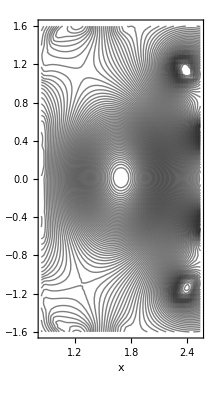

```mathematica
ListContourPlot[zGrid[[;;,;;]],DataRange->{{Min[xGrid],Max[xGrid]},{Min[yGrid],Max[yGrid]}},FrameLabel->{"x","y"},ContourShading->None, Contours->100,AspectRatio->Automatic]
```

```mathematica
dzdxgrid=ParallelTable[df[dx][zGrid[[j,;;]]][rleft][xGrid[[i]]][[4]],{j,Length[yGrid]},{i,Length[xGrid]}];
```

```mathematica
Manipulate[Show[
Plot[{
df[dx][zGrid[[j,;;]]][rleft][x][[4]]/dx,
ListInterpolation[zGrid[[j,;;]],{Min[xGrid],Max[xGrid]}]'[x]
},{x,Min[xGrid],Max[xGrid]},PlotRange->Full,PlotStyle->{Red,Blue}],
ListPlot[{
Transpose[{xGrid,dzdxgrid[[j,;;]]/dx}],
Transpose[{(xGrid[[2;;]]+xGrid[[;;-2]])/2,(zGrid[[j,2;;]]-zGrid[[j,;;-2]])/(xGrid[[2;;]]-xGrid[[;;-2]])}]
},PlotStyle->{Red,Blue}]
],{j,1,Length[yGrid],1}]
```

```mathematica
Dimensions[dzdxgrid]
```

{65,65}

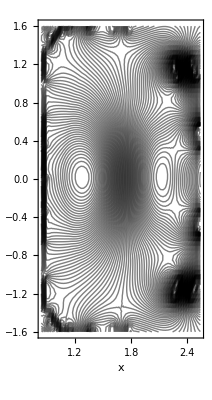

```mathematica
ListContourPlot[dzdxgrid,DataRange->{{Min[xGrid],Max[xGrid]},{Min[yGrid],Max[yGrid]}},FrameLabel->{"x","y"},ContourShading->None, Contours->100,AspectRatio->Automatic]
```

```mathematica
dzdygrid=ParallelTable[df[dy][zGrid[[;;,i]]][zmin][yGrid[[j]]][[4]],{j,Length[yGrid]},{i,Length[xGrid]}];
```

```mathematica
Manipulate[Show[
Plot[{
df[dy][zGrid[[;;,i]]][zmin][y][[4]]/dy,
ListInterpolation[zGrid[[;;,i]],{Min[yGrid],Max[yGrid]}]'[y]
},{y,Min[yGrid],Max[yGrid]},PlotRange->Full,PlotStyle->{Red,Blue}],
ListPlot[{
Transpose[{yGrid,dzdygrid[[;;,i]]/dy}],
Transpose[{(yGrid[[2;;]]+yGrid[[;;-2]])/2,(zGrid[[2;;,i]]-zGrid[[;;-2,i]])/(yGrid[[2;;]]-yGrid[[;;-2]])}]
},PlotStyle->{Red,Blue}]
],{i,1,Length[xGrid],1}]
```

```mathematica
Dimensions[dzdygrid]
```

{65,65}

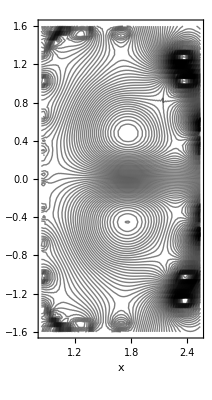

```mathematica
ListContourPlot[dzdygrid,DataRange->{{Min[xGrid],Max[xGrid]},{Min[yGrid],Max[yGrid]}},FrameLabel->{"x","y"},ContourShading->None, Contours->100,AspectRatio->Automatic]
```

```mathematica
dzdxygrid=ParallelTable[df[dx][dzdygrid[[j,;;]]][rleft][xGrid[[i]]][[4]],{j,Length[yGrid]},{i,Length[xGrid]}];
```

```mathematica
Manipulate[Show[
Plot[df[dx][dzdygrid[[j,;;]]][rleft][x][[4]],{x,Min[xGrid],Max[xGrid]}],
ListPlot[Transpose[{xGrid,dzdxygrid[[j,;;]]}]]
],{j,1,Length[yGrid],1}]
```

```mathematica
Dimensions[dzdxygrid]
```

{65,65}

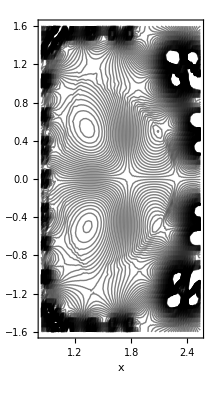

```mathematica
ListContourPlot[dzdxygrid,DataRange->{{Min[xGrid],Max[xGrid]},{Min[yGrid],Max[yGrid]}},FrameLabel->{"x","y"},ContourShading->None, Contours->100,AspectRatio->Automatic]
```

```mathematica
dzdxygrid2=ParallelTable[df[dy][dzdxgrid[[;;,i]]][zmin][yGrid[[j]]][[4]],{j,Length[yGrid]},{i,Length[xGrid]}];
```

```mathematica
Manipulate[Show[
Plot[df[dy][dzdxgrid[[;;,i]]][zmin][y][[4]],{y,Min[yGrid],Max[yGrid]}],
ListPlot[Transpose[{yGrid,dzdxygrid2[[;;,i]]}]]
],{i,1,Length[xGrid],1}]
```

```mathematica
Dimensions[dzdxygrid2]
```

{65,65}

```mathematica
ListContourPlot[dzdxygrid2,DataRange->{{Min[xGrid],Max[xGrid]},{Min[yGrid],Max[yGrid]}},FrameLabel->{"x","y"},ContourShading->None, Contours->100,AspectRatio->Automatic]
```

-Graphics-

```mathematica
fmatrix[f_,dx_,dy_,dxdy_][i_,j_]:={
{f[[j,i]],f[[j+1,i]],dy[[j,i]],dy[[j+1,i]]},
{f[[j,i+1]],f[[j+1,i+1]],dy[[j,i+1]],dy[[j+1,i+1]]},
{dx[[j,i]],dx[[j+1,i]],dxdy[[j,i]],dxdy[[j+1,i]]},
{dx[[j,i+1]],dx[[j+1,i+1]],dxdy[[j,i+1]],dxdy[[j+1,i+1]]}
}
```

```mathematica
left={
{1,0,0,0},
{0,0,1,0},
{-3,3,-2,-1},
{2,-2,1,1}
};
```

```mathematica
right={
{1,0,-3,2},
{0,0,3,-2},
{0,1,-2,1},
{0,0,-1,1}
};
```

```mathematica
a[i_,j_]:=left.fmatrix[zGrid,dzdxgrid,dzdygrid,dzdxygrid][i,j].right;
```

```mathematica
Dimensions[Table[1,10,5]]
```

{10,5}

```mathematica
coefficents=ParallelTable[a[i,j],{i,Length[xGrid]-1},{j,Length[yGrid]-1}];
```

```mathematica
igrid=Table[i-1,{i,Length[zGrid[[1]]]-1}];
jgrid=Table[j-1,{j,Length[zGrid]-1}];
```

```mathematica
Dimensions[coefficents]
```

{64,64,4,4}

```mathematica
cSym={
{c00,c01,c02,c03},
{c10,c11,c12,c13},
{c20,c21,c22,c23},
{c30,c31,c32,c33}
}
```

{{c00,c01,c02,c03},{c10,c11,c12,c13},{c20,c21,c22,c23},{c30,c31,c32,c33}}

```mathematica
csym2d={
Sum[If[i-1<=0,1,(-ip)^(i-1)]*If[j-1<=0,1,(-jp)^(j-1)]*cSym[[i,j]],{i,4},{j,4}],
Sum[(i-1)*If[i-2<=0,1,(-ip)^(i-2)]*If[j-1<=0,1,(-jp)^(j-1)]*cSym[[i,j]],{i,4},{j,4}],
Sum[(j-1)*If[i-1<=0,1,(-ip)^(i-1)]*If[j-2<=0,1,(-jp)^(j-2)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[2*(i-1)-3,0]*If[i-3<=0,1,(-ip)^(i-3)]*If[j-1<=0,1,(-jp)^(j-1)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[2*(j-1)-3,0]*If[i-1<=0,1,(-ip)^(i-1)]*If[j-3<=0,1,(-jp)^(j-3)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[i-3,0]*If[i-4<=0,1,(-ip)^(i-4)]*If[j-1<=0,1,(-jp)^(j-1)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[j-3,0]*If[i-1<=0,1,(-ip)^(i-1)]*If[j-4<=0,1,(-jp)^(j-4)]*cSym[[i,j]],{i,4},{j,4}],
Sum[(i-1)*(j-1)*If[i-2<=0,1,(-ip)^(i-2)]*If[j-2<=0,1,(-jp)^(j-2)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[2*(i-1)-3,0]*(j-1)*If[i-3<=0,1,(-ip)^(i-3)]*If[j-2<=0,1,(-jp)^(j-2)]*cSym[[i,j]],{i,4},{j,4}],
Sum[(i-1)*Max[2*(j-1)-3,0]*If[i-2<=0,1,(-ip)^(i-2)]*If[j-3<=0,1,(-jp)^(j-3)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[i-3,0]*(j-1)*If[i-4<=0,1,(-ip)^(i-4)]*If[j-2<=0,1,(-jp)^(j-2)]*cSym[[i,j]],{i,4},{j,4}],
Sum[(i-1)*Max[j-3,0]*If[i-2<=0,1,(-ip)^(i-2)]*If[j-4<=0,1,(-v)^(j-4)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[2*(i-1)-3,0]*Max[2*(j-1)-3,0]*If[i-3<=0,1,(-ip)^(i-3)]*If[j-3<=0,1,(-jp)^(j-3)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[i-3,0]*Max[2*(j-1)-3,0]*If[i-4<=0,1,(-ip)^(i-4)]*If[j-3<=0,1,(-jp)^(j-3)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[2*(i-1)-3,0]*Max[j-3,0]*If[i-3<=0,1,(-ip)^(i-3)]*If[j-4<=0,1,(-jp)^(j-4)]*cSym[[i,j]],{i,4},{j,4}],
Sum[Max[i-3,0]*Max[j-3,0]*If[i-4<=0,1,(-ip)^(i-4)]*If[j-4<=0,1,(-jp)^(j-4)]*cSym[[i,j]],{i,4},{j,4}]
};
```

```mathematica
csym2d//MatrixForm
```

(c00-c10 ip+c20 ip^2-c30 ip^3-c01 jp+c11 ip jp-c21 ip^2 jp+c31 ip^3 jp+c02 jp^2-c12 ip jp^2+c22 ip^2 jp^2-c32 ip^3 jp^2-c03 jp^3+c13 ip jp^3-c23 ip^2 jp^3+c33 ip^3 jp^3
c10-2 c20 ip+3 c30 ip^2-c11 jp+2 c21 ip jp-3 c31 ip^2 jp+c12 jp^2-2 c22 ip jp^2+3 c32 ip^2 jp^2-c13 jp^3+2 c23 ip jp^3-3 c33 ip^2 jp^3
c01-c11 ip+c21 ip^2-c31 ip^3-2 c02 jp+2 c12 ip jp-2 c22 ip^2 jp+2 c32 ip^3 jp+3 c03 jp^2-3 c13 ip jp^2+3 c23 ip^2 jp^2-3 c33 ip^3 jp^2
c20-3 c30 ip-c21 jp+3 c31 ip jp+c22 jp^2-3 c32 ip jp^2-c23 jp^3+3 c33 ip jp^3
c02-c12 ip+c22 ip^2-c32 ip^3-3 c03 jp+3 c13 ip jp-3 c23 ip^2 jp+3 c33 ip^3 jp
c30-c31 jp+c32 jp^2-c33 jp^3
c03-c13 ip+c23 ip^2-c33 ip^3
c11-2 c21 ip+3 c31 ip^2-2 c12 jp+4 c22 ip jp-6 c32 ip^2 jp+3 c13 jp^2-6 c23 ip jp^2+9 c33 ip^2 jp^2
c21-3 c31 ip-2 c22 jp+6 c32 ip jp+3 c23 jp^2-9 c33 ip jp^2
c12-2 c22 ip+3 c32 ip^2-3 c13 jp+6 c23 ip jp-9 c33 ip^2 jp
c31-2 c32 jp+3 c33 jp^2
c13-2 c23 ip+3 c33 ip^2
c22-3 c32 ip-3 c23 jp+9 c33 ip jp
c32-3 c33 jp
c23-3 c33 ip
c33)

```mathematica
{1,xnorm-ip,(xnorm-ip)^2,(xnorm-ip)^3}.({
{c00,c01,c02,c03},
{c10,c11,c22,c13},
{c20,c21,c22,c23},
{c30,c31,c32,c33}
}.{1,(ynorm-jp),(ynorm-jp)^2,(ynorm-jp)^3})//Expand
```

c00-c10 ip+c20 ip^2-c30 ip^3-c01 jp+c11 ip jp-c21 ip^2 jp+c31 ip^3 jp+c02 jp^2-c22 ip jp^2+c22 ip^2 jp^2-c32 ip^3 jp^2-c03 jp^3+c13 ip jp^3-c23 ip^2 jp^3+c33 ip^3 jp^3+c10 xnorm-2 c20 ip xnorm+3 c30 ip^2 xnorm-c11 jp xnorm+2 c21 ip jp xnorm-3 c31 ip^2 jp xnorm+c22 jp^2 xnorm-2 c22 ip jp^2 xnorm+3 c32 ip^2 jp^2 xnorm-c13 jp^3 xnorm+2 c23 ip jp^3 xnorm-3 c33 ip^2 jp^3 xnorm+c20 xnorm^2-3 c30 ip xnorm^2-c21 jp xnorm^2+3 c31 ip jp xnorm^2+c22 jp^2 xnorm^2-3 c32 ip jp^2 xnorm^2-c23 jp^3 xnorm^2+3 c33 ip jp^3 xnorm^2+c30 xnorm^3-c31 jp xnorm^3+c32 jp^2 xnorm^3-c33 jp^3 xnorm^3+c01 ynorm-c11 ip ynorm+c21 ip^2 ynorm-c31 ip^3 ynorm-2 c02 jp ynorm+2 c22 ip jp ynorm-2 c22 ip^2 jp ynorm+2 c32 ip^3 jp ynorm+3 c03 jp^2 ynorm-3 c13 ip jp^2 ynorm+3 c23 ip^2 jp^2 ynorm-3 c33 ip^3 jp^2 ynorm+c11 xnorm ynorm-2 c21 ip xnorm ynorm+3 c31 ip^2 xnorm ynorm-2 c22 jp xnorm ynorm+4 c22 ip jp xnorm ynorm-6 c32 ip^2 jp xnorm ynorm+3 c13 jp^2 xnorm ynorm-6 c23 ip jp^2 xnorm ynorm+9 c33 ip^2 jp^2 xnorm ynorm+c21 xnorm^2 ynorm-3 c31 ip xnorm^2 ynorm-2 c22 jp xnorm^2 ynorm+6 c32 ip jp xnorm^2 ynorm+3 c23 jp^2 xnorm^2 ynorm-9 c33 ip jp^2 xnorm^2 ynorm+c31 xnorm^3 ynorm-2 c32 jp xnorm^3 ynorm+3 c33 jp^2 xnorm^3 ynorm+c02 ynorm^2-c22 ip ynorm^2+c22 ip^2 ynorm^2-c32 ip^3 ynorm^2-3 c03 jp ynorm^2+3 c13 ip jp ynorm^2-3 c23 ip^2 jp ynorm^2+3 c33 ip^3 jp ynorm^2+c22 xnorm ynorm^2-2 c22 ip xnorm ynorm^2+3 c32 ip^2 xnorm ynorm^2-3 c13 jp xnorm ynorm^2+6 c23 ip jp xnorm ynorm^2-9 c33 ip^2 jp xnorm ynorm^2+c22 xnorm^2 ynorm^2-3 c32 ip xnorm^2 ynorm^2-3 c23 jp xnorm^2 ynorm^2+9 c33 ip jp xnorm^2 ynorm^2+c32 xnorm^3 ynorm^2-3 c33 jp xnorm^3 ynorm^2+c03 ynorm^3-c13 ip ynorm^3+c23 ip^2 ynorm^3-c33 ip^3 ynorm^3+c13 xnorm ynorm^3-2 c23 ip xnorm ynorm^3+3 c33 ip^2 xnorm ynorm^3+c23 xnorm^2 ynorm^3-3 c33 ip xnorm^2 ynorm^3+c33 xnorm^3 ynorm^3

```mathematica
{1,xnorm,xnorm^2,xnorm^3}.(Transpose[{
{c00,c01,c02,c03},
{c10,c11,c22,c13},
{c20,c21,c22,c23},
{c30,c31,c32,c33}
}].{1,ynorm,ynorm^2,ynorm^3})//Expand
```

c00+c01 xnorm+c02 xnorm^2+c03 xnorm^3+c10 ynorm+c11 xnorm ynorm+c22 xnorm^2 ynorm+c13 xnorm^3 ynorm+c20 ynorm^2+c21 xnorm ynorm^2+c22 xnorm^2 ynorm^2+c23 xnorm^3 ynorm^2+c30 ynorm^3+c31 xnorm ynorm^3+c32 xnorm^2 ynorm^3+c33 xnorm^3 ynorm^3

```mathematica
{1,xnorm,xnorm^2,xnorm^3}.({
{csym2d[[1]],csym2d[[3]],csym2d[[5]],csym2d[[7]]},
{csym2d[[2]],csym2d[[8]],csym2d[[10]],csym2d[[12]]},
{csym2d[[4]],csym2d[[9]],csym2d[[13]],csym2d[[15]]},
{csym2d[[6]],csym2d[[11]],csym2d[[14]],csym2d[[16]]}
}.{1,ynorm,ynorm^2,ynorm^3})-{1,xnorm-ip,(xnorm-ip)^2,(xnorm-ip)^3}.({
{c00,c01,c02,c03},
{c10,c11,c12,c13},
{c20,c21,c22,c23},
{c30,c31,c32,c33}
}.{1,(ynorm-jp),(ynorm-jp)^2,(ynorm-jp)^3})//Expand
```

0

```mathematica
c2d={
Sum[Table[If[i-1<=0,1,(-ip+1)^(i-1)]*If[j-1<=0,1,(-jp+1)^(j-1)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[(i-1)*If[i-2<=0,1,(-ip+1)^(i-2)]*If[j-1<=0,1,(-jp+1)^(j-1)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[(j-1)*If[i-1<=0,1,(-ip+1)^(i-1)]*If[j-2<=0,1,(-jp+1)^(j-2)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[2*(i-1)-3,0]*If[i-3<=0,1,(-ip+1)^(i-3)]*If[j-1<=0,1,(-jp+1)^(j-1)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[2*(j-1)-3,0]*If[i-1<=0,1,(-ip+1)^(i-1)]*If[j-3<=0,1,(-jp+1)^(j-3)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[i-3,0]*If[i-4<=0,1,(-ip+1)^(i-4)]*If[j-1<=0,1,(-jp+1)^(j-1)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[j-3,0]*If[i-1<=0,1,(-ip+1)^(i-1)]*If[j-4<=0,1,(-jp+1)^(j-4)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[(i-1)*(j-1)*If[i-2<=0,1,(-ip+1)^(i-2)]*If[j-2<=0,1,(-jp+1)^(j-2)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[2*(i-1)-3,0]*(j-1)*If[i-3<=0,1,(-ip+1)^(i-3)]*If[j-2<=0,1,(-jp+1)^(j-2)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[(i-1)*Max[2*(j-1)-3,0]*If[i-2<=0,1,(-ip+1)^(i-2)]*If[j-3<=0,1,(-jp+1)^(j-3)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[i-3,0]*(j-1)*If[i-4<=0,1,(-ip+1)^(i-4)]*If[j-2<=0,1,(-jp+1)^(j-2)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[(i-1)*Max[j-3,0]*If[i-2<=0,1,(-ip+1)^(i-2)]*If[j-4<=0,1,(-jp+1)^(j-4)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[yGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[2*(i-1)-3,0]*Max[2*(j-1)-3,0]*If[i-3<=0,1,(-ip+1)^(i-3)]*If[j-3<=0,1,(-jp+1)^(j-3)]*coefficents[[ip,jp,i,j]],{ip,Length[yGrid]-1},{jp,Length[xGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[i-3,0]*Max[2*(j-1)-3,0]*If[i-4<=0,1,(-ip+1)^(i-4)]*If[j-3<=0,1,(-jp+1)^(j-3)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[xGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[2*(i-1)-3,0]*Max[j-3,0]*If[i-3<=0,1,(-ip+1)^(i-3)]*If[j-4<=0,1,(-jp+1)^(j-4)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[xGrid]-1}],{i,4},{j,4}],
Sum[Table[Max[i-3,0]*Max[j-3,0]*If[i-4<=0,1,(-ip+1)^(i-4)]*If[j-4<=0,1,(-jp+1)^(j-4)]*coefficents[[ip,jp,i,j]],{ip,Length[xGrid]-1},{jp,Length[xGrid]-1}],{i,4},{j,4}]
};
```

```mathematica
f2[xmin_,ymin_][x_,y_]:=Module[{ilow,xnorm,jlow,ynorm,a},
ilow=Max[Min[Floor[(x-xmin)/dx],Length[xGrid]-2],0];
xnorm=(x-xmin)/dx;
jlow=Max[Min[Floor[(y-ymin)/dy],Length[yGrid]-2],0];
ynorm=(y-ymin)/dy;
a={
{c2d[[1,ilow+1,jlow+1]],c2d[[3,ilow+1,jlow+1]],c2d[[5,ilow+1,jlow+1]],c2d[[7,ilow+1,jlow+1]]},
{c2d[[2,ilow+1,jlow+1]],c2d[[8,ilow+1,jlow+1]],c2d[[10,ilow+1,jlow+1]],c2d[[12,ilow+1,jlow+1]]},
{c2d[[4,ilow+1,jlow+1]],c2d[[9,ilow+1,jlow+1]],c2d[[13,ilow+1,jlow+1]],c2d[[15,ilow+1,jlow+1]]},
{c2d[[6,ilow+1,jlow+1]],c2d[[11,ilow+1,jlow+1]],c2d[[14,ilow+1,jlow+1]],c2d[[16,ilow+1,jlow+1]]}
};
{
{dx,ilow,xnorm},
{dy,jlow,ynorm},
{1,xnorm,xnorm^2,xnorm^3}.(a.{1,ynorm,ynorm^2,ynorm^3}),
a//MatrixForm
}
];
```

```mathematica
f2dx[xmin_,ymin_][x_,y_]:=Module[{ilow,xnorm,jlow,ynorm,a},
ilow=Max[Min[Floor[(x-xmin)/dx],Length[xGrid]-2],0];
xnorm=(x-xmin)/dx;
jlow=Max[Min[Floor[(y-ymin)/dy],Length[yGrid]-2],0];
ynorm=(y-ymin)/dy;
a={
{c2d[[2,ilow+1,jlow+1]],c2d[[8,ilow+1,jlow+1]],c2d[[10,ilow+1,jlow+1]],c2d[[12,ilow+1,jlow+1]]},
{c2d[[4,ilow+1,jlow+1]],c2d[[9,ilow+1,jlow+1]],c2d[[13,ilow+1,jlow+1]],c2d[[15,ilow+1,jlow+1]]},
{c2d[[6,ilow+1,jlow+1]],c2d[[11,ilow+1,jlow+1]],c2d[[14,ilow+1,jlow+1]],c2d[[16,ilow+1,jlow+1]]}
};
{
{dx,ilow,xnorm},
{dy,jlow,ynorm},
({1,2*xnorm,3*xnorm^2}/dx).(a.{1,ynorm,ynorm^2,ynorm^3}),
a//MatrixForm
}
];
```

```mathematica
f2dy[xmin_,ymin_][x_,y_]:=Module[{ilow,xnorm,jlow,ynorm,a},
ilow=Max[Min[Floor[(x-xmin)/dx],Length[xGrid]-2],0];
xnorm=(x-xmin)/dx;
jlow=Max[Min[Floor[(y-ymin)/dy],Length[yGrid]-2],0];
ynorm=(y-ymin)/dy;
a={
{c2d[[3,ilow+1,jlow+1]],c2d[[5,ilow+1,jlow+1]],c2d[[7,ilow+1,jlow+1]]},
{c2d[[8,ilow+1,jlow+1]],c2d[[10,ilow+1,jlow+1]],c2d[[12,ilow+1,jlow+1]]},
{c2d[[9,ilow+1,jlow+1]],c2d[[13,ilow+1,jlow+1]],c2d[[15,ilow+1,jlow+1]]},
{c2d[[11,ilow+1,jlow+1]],c2d[[14,ilow+1,jlow+1]],c2d[[16,ilow+1,jlow+1]]}
};
{
{dx,ilow,xnorm},
{dy,jlow,ynorm},
{1,xnorm,xnorm^2,xnorm^3}.(a.({1,2*ynorm,3*ynorm^2}/dy)),
a//MatrixForm
}
];
```

```mathematica
ans=Solve[{
zmin==mp*rleft+bp,
zmax==mp*rmax+bp
},{mp,bp}][[1]]
```

{mp→1.88235,bp→-3.18118}

```mathematica
zcoodinate[x_]:=mp*x+bp/.ans;
```

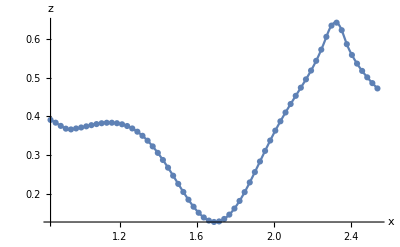

```mathematica
Show[
Plot[f2[rleft,zmin][x,zcoodinate[x]][[3]],{x,Min[xGrid],Max[xGrid]},AxesLabel->{"x","z"},PlotPoints->200],
ListPlot[Transpose[{xGrid,Table[zGrid[[i,i]],{i,Length[xGrid]}]}]]
]
```

```mathematica
temp=f2[rleft,zmin][rleft+64*dx,zmin];
```

```mathematica
temp[[4]]//MatrixForm
```

(-10.8239 | -2.42889 | -3.08411×10^-10 | -0.0687112
0.530975 | 0.114855 | 1.45411×10^-11 | 0.00327124
-0.00830813 | -0.00179791 | -2.28515×10^-13 | -0.0000514495
0.0000432715 | 9.3641×10^-6 | 1.19696×10^-15 | 2.67966×10^-7)

```mathematica
temp[[1]]
temp[[2]]
```

{0.0265625,63,64.}

{0.05,0,0.}

```mathematica
Manipulate[
Show[
Plot[f2[rleft,zmin][x,yGrid[[j]]][[3]],{x,Min[xGrid],Max[xGrid]},AxesLabel->{"x","z"},PlotPoints->200],
ListPlot[Transpose[{xGrid,zGrid[[j,;;]]}]]
],{j,1,Length[yGrid],1}]
```

```mathematica
ListPlot3D[zGrid,DataRange->{{Min[xGrid],Max[xGrid]},{Min[yGrid],Max[yGrid]}}]
```

-Graphics3D-

```mathematica
Plot3D[f2[rleft,zmin][x,y][[3]],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},AxesLabel->{"x","y","z"},PlotPoints->400]
```

-Graphics3D-

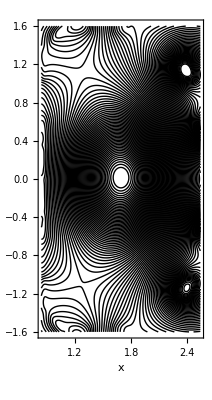

```mathematica
ContourPlot[f2[rleft,zmin][x,y][[3]],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},ContourShading->None, Contours->100,AspectRatio->Automatic,PlotPoints->200]
```

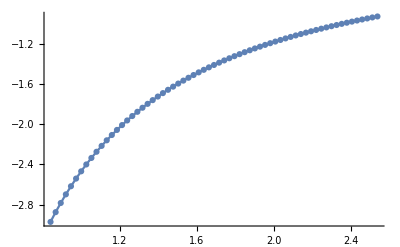

```mathematica
Show[
Plot[f[dx][fpol/xGrid][rleft][x][[4]],{x,Min[xGrid],Max[xGrid]}],
ListPlot[Transpose[{xGrid,fpol/xGrid}]]
]
```

```mathematica
dpsi=(psibry-Min[psi])/(65-1)
```

0.00386779

```mathematica
numpsi=Ceiling[(Max[psi]-Min[psi])/dpsi]+1
```

139

```mathematica
psi1D=Subdivide[Min[psi],Max[psi],numpsi-1];
```

```mathematica
psi1D[[2]]-psi1D[[1]]
```

0.00386395

```mathematica
profile[s_]:=If[s>1,0,(1-s^5.0)^2.0];
```

```mathematica
ans2=Solve[{0,1}==mp*{Min[psi1D],psibry}+bp,{mp,bp}][[1]];
```

```mathematica
psinorm=Map[mp*#+bp&,psi1D]/.ans2;
```

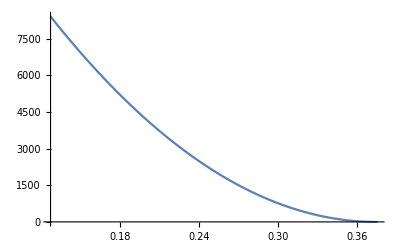

```mathematica
Show[
Plot[f[dpsi][pres][Min[psi]][x][[4]],{x,Min[psi],psibry}]
]
```

```mathematica
predGrid=Map[If[#>psibry,0,f[dpsi][pres][Min[psi]][#][[4]]]&,psi1D]/Max[pres];
```

```mathematica
factor=Map[If[#>psibry,0,1]&,psi1D][[;;-2]];
```

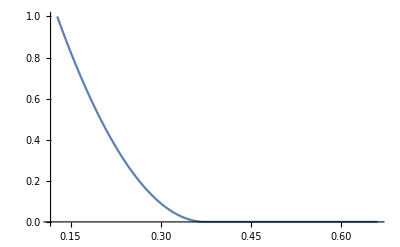

```mathematica
ListLinePlot[Transpose[{psi1D,predGrid}]]
```

```mathematica
Min[psinorm]
```

0.

```mathematica
Max[psinorm]
```

2.15411

```mathematica
neGrid=Map[profile[#]&,psinorm];
teGrid=Map[profile[#]&,psinorm];
```

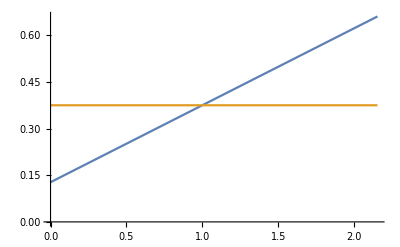

```mathematica
ListLinePlot[{Transpose[{psinorm,psi1D}],{{Min[psinorm],psibry},{Max[psinorm],psibry}}}]
```

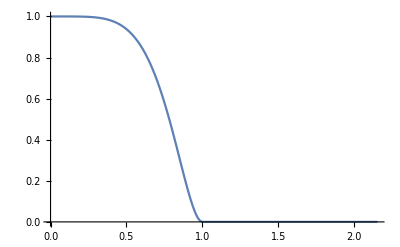

```mathematica
ListLinePlot[Transpose[{psinorm,neGrid}]]
```

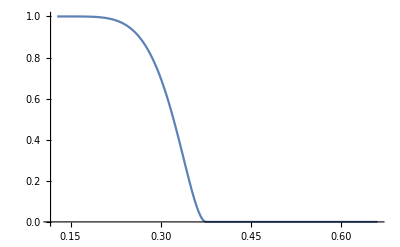

```mathematica
ListLinePlot[Transpose[{psi1D,neGrid}]]
```

```mathematica
MinMax[neGrid]
```

{0,1.}

```mathematica
MinMax[psi]
```

{0.12769,0.660916}

```mathematica
ListLinePlot[Transpose[{psi1D,teGrid}]]
```

-Graphics-

```mathematica
MinMax[teGrid]
```

{0,1.}

```mathematica
fpolc=c1D[fpol];
```

```mathematica
presc=Map[#*factor&,c1D[predGrid]];
```

```mathematica
nec=Map[#*factor&,c1D[neGrid]];
```

```mathematica
tec=Map[#*factor&,c1D[teGrid]];
```

```mathematica
Dimensions[c2d]
```

{16,64,64}

```mathematica
Length[fpolc[[1]]]
```

64

```mathematica
Dimensions[c2d[[1]]]
```

{64,64}

```mathematica
Length[tec[[1]]]
```

138

```mathematica
Export["efit.nc",{
"Dimensions"->{
"numr"->64,
"numz"->64,
"numpsi"->numpsi-1
},
"Datasets"->{
"rmin"->{"Data"->rleft},
"dr"->{"Data"->xGrid[[2]]-xGrid[[1]]},
"zmin"->{"Data"->zmin},
"dz"->{"Data"->yGrid[[2]]-yGrid[[1]]},
"psimin"->{"Data"->Min[psi]},
"psibry"->{"Data"->psibry},
"dpsi"->{"Data"->psi1D[[2]]-psi1D[[1]]},
"fpol_c0"->{"Data"->fpolc[[1]],"DimensionNames"->"numr"},
"fpol_c1"->{"Data"->fpolc[[2]],"DimensionNames"->"numr"},
"fpol_c2"->{"Data"->fpolc[[3]],"DimensionNames"->"numr"},
"fpol_c3"->{"Data"->fpolc[[4]],"DimensionNames"->"numr"},
"pres_scale"->{"Data"->Max[pres]},
"pressure_c0"->{"Data"->presc[[1]],"DimensionNames"->"numpsi"},
"pressure_c1"->{"Data"->presc[[2]],"DimensionNames"->"numpsi"},
"pressure_c2"->{"Data"->presc[[3]],"DimensionNames"->"numpsi"},
"pressure_c3"->{"Data"->presc[[4]],"DimensionNames"->"numpsi"},
"ne_scale"->{"Data"->Max[ne]},
"ne_c0"->{"Data"->nec[[1]],"DimensionNames"->"numpsi"},
"ne_c1"->{"Data"->nec[[2]],"DimensionNames"->"numpsi"},
"ne_c2"->{"Data"->nec[[3]],"DimensionNames"->"numpsi"},
"ne_c3"->{"Data"->nec[[4]],"DimensionNames"->"numpsi"},
"te_scale"->{"Data"->Max[te]},
"te_c0"->{"Data"->tec[[1]],"DimensionNames"->"numpsi"},
"te_c1"->{"Data"->tec[[2]],"DimensionNames"->"numpsi"},
"te_c2"->{"Data"->tec[[3]],"DimensionNames"->"numpsi"},
"te_c3"->{"Data"->tec[[4]],"DimensionNames"->"numpsi"},
"psi_c00"->{"Data"->c2d[[1]],"DimensionNames"->{"numz","numr"}},
"psi_c10"->{"Data"->c2d[[2]],"DimensionNames"->{"numz","numr"}},
"psi_c01"->{"Data"->c2d[[3]],"DimensionNames"->{"numz","numr"}},
"psi_c20"->{"Data"->c2d[[4]],"DimensionNames"->{"numz","numr"}},
"psi_c02"->{"Data"->c2d[[5]],"DimensionNames"->{"numz","numr"}},
"psi_c30"->{"Data"->c2d[[6]],"DimensionNames"->{"numz","numr"}},
"psi_c03"->{"Data"->c2d[[7]],"DimensionNames"->{"numz","numr"}},
"psi_c11"->{"Data"->c2d[[8]],"DimensionNames"->{"numz","numr"}},
"psi_c21"->{"Data"->c2d[[9]],"DimensionNames"->{"numz","numr"}},
"psi_c12"->{"Data"->c2d[[10]],"DimensionNames"->{"numz","numr"}},
"psi_c31"->{"Data"->c2d[[11]],"DimensionNames"->{"numz","numr"}},
"psi_c13"->{"Data"->c2d[[12]],"DimensionNames"->{"numz","numr"}},
"psi_c22"->{"Data"->c2d[[13]],"DimensionNames"->{"numz","numr"}},
"psi_c32"->{"Data"->c2d[[14]],"DimensionNames"->{"numz","numr"}},
"psi_c23"->{"Data"->c2d[[15]],"DimensionNames"->{"numz","numr"}},
"psi_c33"->{"Data"->c2d[[16]],"DimensionNames"->{"numz","numr"}}
}},"Rules"]
```

efit.nc

## Ray Result

```mathematica
rayfile=SystemDialogInput["FileOpen"]
```

/Users/m4c/Desktop/RayPath.xlsx

```mathematica
data=Normal[Import[rayfile,"Data"]][[1]];
```

```mathematica
fne[r_,z_]:=Max[ne]*f[dpsi][neGrid][Min[psi]][f2[rleft,zmin][r,z][[3]]][[4]];
```

```mathematica
q=1.602176634*^-19
me=9.1093837015*^-31
ϵ0=8.8541878138*^-12
μ0=Pi*4.0*^-7
c=1/Sqrt[ϵ0*μ0]
```

1.60218×10^-19

9.10938×10^-31

8.85419×10^-12

1.25664×10^-6

2.99792×10^8

```mathematica
ωpe[r_,z_]:=Sqrt[fne[r,z]*q*q/(ϵ0*me*c*c)];
```

```mathematica
bvec[r_,z_]:={
f2dy[rleft,zmin][r,z][[3]]/r,
f[dx][fpol][rleft][r][[4]]/r,
-f2dx[rleft,zmin][r,z][[3]]/r
};
```

```mathematica
bmod[r_,z_]:=Sqrt[bvec[r,z].bvec[r,z]];■_□
```

```mathematica
bhat[r_,z_]:=bvec[r,z]/bmod[r,z];
```

```mathematica
Ωce[r_,z_]:=q*bmod[r,z]/(me*c);
```

```mathematica
ω=1036.81;(*data[[1,2]];*)
```

```mathematica
ωr[r_,z_]:=0.5*(Ωce[r,z]+Sqrt[Ωce[r,z]^2+4*ωpe[r,z]^2]);
ωl[r_,z_]:=0.5*(-Ωce[r,z]+Sqrt[Ωce[r,z]^2+4*ωpe[r,z]^2]);
```

```mathematica
ωh[r_,z_]:=Sqrt[Ωce[r,z]^2+ωpe[r,z]^2];
```

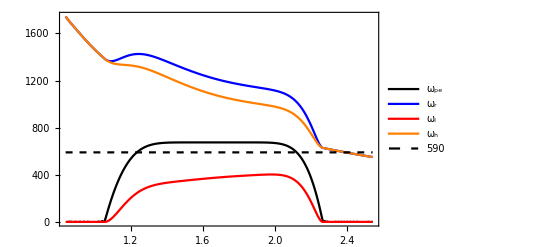

```mathematica
Plot[{
ωpe[x,0.0],
ωr[x,0.0],
ωl[x,0.0],
ωh[x,0.0],
ω
},{x,Min[xGrid],Max[xGrid]},PlotStyle->{Black,Blue,Red,Orange,Directive[Dashed,Black]},Frame->True,ImageSize->Full,PlotLegends->{"ω_pe","ω_r","ω_l","ω_h",ω}]
```

```mathematica
Show[
DensityPlot[fne[x,y],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},AspectRatio->Automatic,ImageSize->Full,PlotLegends->Automatic],
ContourPlot[f2[rleft,zmin][x,y][[3]],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},ContourShading->None, Contours->100,AspectRatio->Automatic,PlotPoints->200,ImageSize->Full],
ContourPlot[f2[rleft,zmin][x,y][[3]],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},ContourShading->None, Contours->{psibry},AspectRatio->Automatic,PlotPoints->200,ContourStyle->White],
ListLinePlot[{
Transpose[{data[[;;,6]],data[[;;,8]]}],
Transpose[{data[[;;,15]],data[[;;,17]]}],
Transpose[{data[[;;,24]],data[[;;,26]]}]
},PlotStyle->Red],
ContourPlot[ωpe[x,y],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},ContourShading->None, Contours->{ω},AspectRatio->Automatic,ContourStyle->Directive[Thick, Black, Dashed]],
ContourPlot[ωr[x,y],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},ContourShading->None, Contours->{ω},AspectRatio->Automatic,ContourStyle->Directive[Thick, Blue, Dashed]],
ContourPlot[ωl[x,y],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},ContourShading->None, Contours->{ω},AspectRatio->Automatic,ContourStyle->Directive[Thick, White, Dashed]],
ContourPlot[ωh[x,y],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},ContourShading->None, Contours->{ω},AspectRatio->Automatic,ContourStyle->Directive[Thick, Green, Dashed]],
VectorPlot[bvec[x,y][[1;;3;;2]],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},VectorPoints->100,VectorColorFunction->None,VectorStyle->White]
]
```

-Graphics-

```mathematica
kvec={0.0,0.0,0.0};
```

```mathematica
n=kvec/ω;
```

```mathematica
nperp[x_,y_]:=Cross[bhat[x,y],n];
```

```mathematica
nperp[2.5,0.0]
```

{0.,0.,0.}

```mathematica
dispersion[x_,y_]:=1-ωpe[x,y]^2/ω^2-nperp[x,y]*nperp[x,y];
```

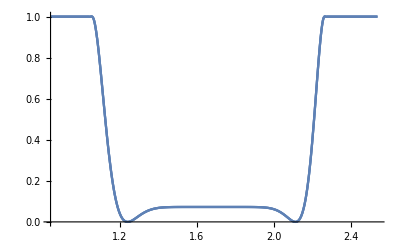

```mathematica
Plot[dispersion[x,0.0]^2,{x,Min[xGrid],Max[xGrid]}]
```

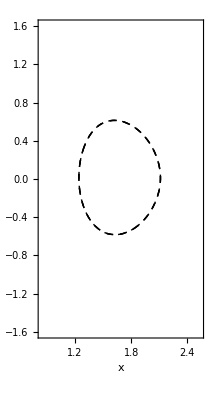

```mathematica
ContourPlot[dispersion[x,y],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},ContourShading->None, Contours->{0},AspectRatio->Automatic,ContourStyle->Directive[Thick, Black, Dashed]]
```

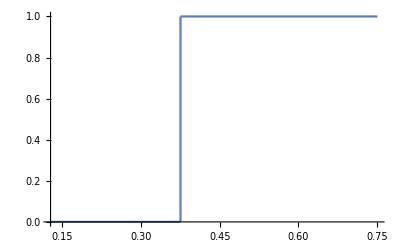

```mathematica
Show[
Plot[Floor[p/psibry],{p,Min[psi],2*psibry}],
ListLinePlot[{{psibry,0},{psibry,1}}]
]
```

```mathematica
DensityPlot[Floor[f2[rleft,zmin][x,y][[3]]/psibry],{x,Min[xGrid],Max[xGrid]},{y,Min[yGrid],Max[yGrid]},FrameLabel->{"x","z"},AspectRatio->Automatic,PlotPoints->200,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Min[psi]
```

0.12769